## 1. Solving TOV equations.

### 1.1 Equation of state:

#### 1.1.1 Relativistic Case (pure NS)

Let’s try first just this one: relativistic case

```mathematica
Pressure R[ϵ_]:=ϵ/3;
Density R[p_]:=3p;
```

#### 1.1.2 Non Relativistic Case (pure NS)

Pressure and density take the following form

```mathematica
ϵ(P) = 5 (m/(15 π^2 λ^3))^(2/5)P^(3/5)
```

with m, λ of the gas we are considering, let’s say neutrons only, then

```mathematica
mp=1.6726219 10^-24;
mn=1.67 10^-24;
c = 2.99792458 10^10;
lambda=2.1 10^-14;
k =5((mn c^2)/(15 π^2 lambda^3))^(0.4);
(*   Functions:    *)
Density NR[p_]:=k p^0.6
Pressure NR[ϵ_]:= (ϵ/k)^5/3
```

#### 1.1.3 Whole Range Neutron Star (Pure NS)

We need first to define density and pressure as function of non-dimensional fermi momentum

```mathematica
n = mn c^2/(Pi^2*lambda^3);
epsilon[z_]:=n/8 ((2z^3+z)Sqrt[1+z^2]-ArcSinh[z])
pressure[z_]:=n/8((2z^3 /3-z)Sqrt[1+z^2]+ArcSinh[z])
```

now, we create a table of data (p, ϵ):

```mathematica
d1 = Table[{pressure[z],epsilon[z]},{z,10.^-3,10^-2,10^-5}];
d2 =Table[{pressure[z],epsilon[z]},{z,10.^-2,10^-1,10^-4}];
d3=Table[{pressure[z],epsilon[z]},{z,10.^-1,10^0,10^-3}];
d4=Table[{pressure[z],epsilon[z]},{z,10.^0,10^1,10^-2}];
d5=Table[{pressure[z],epsilon[z]},{z,10.^1,10^2,10^-1}];
d6=Table[{pressure[z],epsilon[z]},{z,10.^2,10^3,10^0}];
```

```mathematica
density n=Union[d1,d2,d3,d4,d5,d6];
Density NS = Interpolation[density n,InterpolationOrder->100];
```

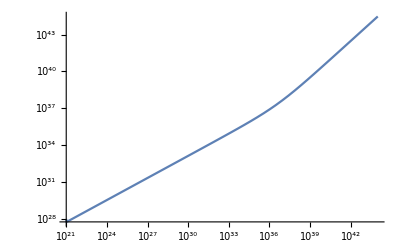

```mathematica
LogLogPlot[Density NS[x],{x,10^21,10^44}]
```

Now, let’s build the function for the whole range as a picewise function taking the R and NR approx,

```mathematica
pw=Piecewise[{{Density NR[x], 0≤  x<10^23}, {Density NS[x],10^23≤ x≤ 10^45},{Density R[x],x>10^45}}];
dener[p_]:=pw/.x-> p
```

#### Constants

We need to declare the following constants

```mathematica
G = 6.6743 10^-8;
Subscript[M, sol]=1.9885 10^33;
c = 2.99792458 10^10;
α=G Subscript[M, sol]/(10^5 c^2);
Subscript[E0, sol]= Subscript[M, sol] c^2;
km3 = (10.0^5)^3;
rmin = 0.001;
rmax = 350;
densup = 7.86;
```

The numerical values of the constants to non-dimensionalise the equations are:

```mathematica
beta[Pc_]:=4 Pi Pc km3 /Subscript[E0, sol]
β =beta[10^35];
{α,β}
```

{1.47669,0.000703142}

Now we can proceed to do the numerical integration

#### Newton Equations:

We solve first this simple case.

```mathematica
Pc = 3.3 10^34;
ListRG={};
Do[
{solutionN = NDSolve[{p'[r]== If[p[r]>0,-(α dener[p[r]*Pc]*M[r])/(Pc r^2),0.0],
M'[r]==If[p[r]>0,(4 π (Pc km3)/Subscript[E0, sol]) r^2 dener[p[r] Pc]/Pc,0.0],p[rmin]==1,M[rmin]==0.0},{p,M},{r,rmin,rad},MaxSteps->Infinity];
mass ad[x_]:=M[x]/.solutionN[[1]];
pressure ad[x_]:=p[x]/.solutionN[[1]];
If[pressure ad[rad]==0,
Break[],
ListRG=Append[ListRG,{rad,dener[Pc*pressure ad[rad]]}]
];
},
{rad,rmin+0.1,25,.1}]
```

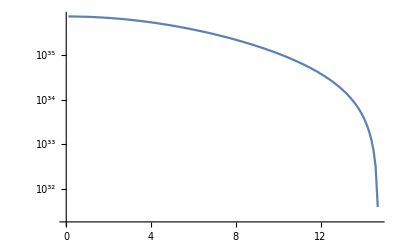

```mathematica
ListLogPlot[ListRG,Joined->True]
```

```mathematica
lista = {};
Do[{
listaloc = {};
Do[
 listaloc = Append[listaloc, {i,j}],
{i,1,5,1}];
lista = Append[lista, listaloc]},
{j,1,2}]
lista
```

{{{1,1},{2,1},{3,1},{4,1},{5,1}},{{1,2},{2,2},{3,2},{4,2},{5,2}}}

#### TOV Equations:

```mathematica
ListPc ={10^33,10^38};
ListR = Table[0,Length[ListPc]];
ListM = Table[0,Length[ListPc]];
Listmass =Table[0,Length[ListPc]];
Listϵ={};
Listp={};
Do[{
Pc = ListPc[[ñ]];
localp = {};
localϵ = {};
Do[{ 
solutionTOV = NDSolve[
{p'[r]== If[p[r]>0,-α*(M[r]+(4 π (Pc km3)/Subscript[E0, sol])r^3 p[r] )(dener[p[r]*Pc]/Pc+p[r])/(r(r - 2 α  M[r])),0.0],
M'[r]==If[p[r]>0,(4 π (Pc km3)/Subscript[E0, sol]) r^2 dener[p[r] Pc]/Pc,0.0],
p[rmin]==1.0,M[rmin]==0.0},{p,M},{r,rmin,rad},MaxSteps->Infinity];
mass[x_]=M[x]/.solutionTOV[[1]];
TOVpressure[x_]:=p[x]/.solutionTOV[[1]];
Listmass[[ñ]]=mass;
If[TOVpressure[rad]==0,
Break[],
localϵ=Append[localϵ,{rad,dener[Pc*TOVpressure[rad]]/Pc}];
localp=Append[localp,{rad,TOVpressure[rad]}];
ListR[[ñ]]=rad;
ListM[[ñ]]=mass[rad];
];
},{rad,rmin+0.1,15,.1}];
Listϵ = Append[Listϵ, localϵ];
Listp = Append[Listp, localp];
},{ñ,1,Length[ListPc]}]
```

```mathematica
PureNSDensity=ListLogPlot[Listϵ,Joined->True,
Frame->True,
PlotStyle->Red,
FrameLabel->{"r [km]","ρ(r) [g / cm^3]"}]
```

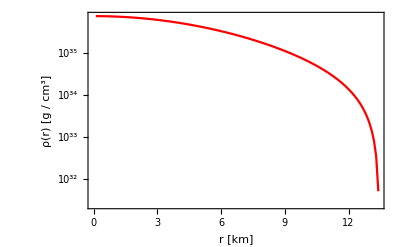

```mathematica
Export["Plots/PureNS_Density.pdf",PureNSDensity];
```

### Gravity Tunnel inside the NS (Pure case)

First, define non dimensional functions for energy density and pressure (they are both in terms of central pressure)

```mathematica
ϵ n=Table[0,Length[ListPc]];
p n=Table[0,Length[ListPc]];
Do[{
ϵ n[[ñ]]= Interpolation[Listϵ[[ñ]],InterpolationOrder->10];
p n[[ñ]] = Interpolation[Listp[[ñ]],InterpolationOrder->10]},{ñ,1,Length[ListPc]}]
```

Along with the non-dimensional mass, this will be useful to define the metric tensor component functions:

```mathematica
Subscript[g, rr](r)=A(r) = (1 - (2 G M(r))/r)^-1 = (1 - 2α (M̄)/r)^-1
```

with M̄ in units of solar masses and r in km. Then

```mathematica
A = Table[0,Length[ListPc]];
Do[{m =Listmass[[ñ]];a[r_]:= (1 - 2 α m[r]/r)^-1; A[[ñ]]=a} ,{ñ,1,Length[ListPc]}]
```

and the other function comes from the diff. eq.

```mathematica
(B'(r))/(B(r))= - (2 P'(r))/(P(r)+ϵ(r))
```

with boundary conditions in the surface equal to the Schwarzschild solution for the exterior metric:

```mathematica
B = Table[0,Length[ListPc]];
Do[{Bmax =1- (2 α)/ListR[[ñ]];
BFunction=NDSolve[ {Bb'[r] == -2 Bb[r] p n[[ñ]]'[r]/(p n[[ñ]][r]+ϵ n[[ñ]][r]),Bb[ListR[[ñ]]]== Bmax},Bb[r],{r,rmin+0.1,ListR[[ñ]]}];
b[r_]=Bb[r]/.BFunction[[1]];
B[[ñ]]=b},{ñ,1,Length[ListPc]}]
```

with  A=g_rr and B=g_tt, we already have all the components of the metric. The general energy diff. eq. is

```mathematica
1/2(dr/dτ)^2+1/2 g^rr(r)(1 - g^tt(r) E^2)c^2=0
```

from this energy-like equation, consider the potential part, at the turning points (r=R),

```mathematica
V(R) = 1/2 g^rr(R)(1 - g^tt(R) E^2)c^2=0
E^2= 1/(g^tt(R))= Subscript[g, tt](R) 
-> E^2 = B(R)
```

we have therefore the following integral:

```mathematica
Δτ = 2/c∫(√(-Subscript[g, tt](r)))/(√(1 - E^2/Subscript[g, rr](r)))ⅆr
Δτ = 2/c(∫_0)^R(√(A(r)B(r)))/(√(B(R)- B(r)))ⅆr
```

```mathematica
τsNS =2 NIntegrate[Sqrt[A[[2]][r] B[[2]][r]/(B[[1]][ListR[[2]]]-B[[2]][r])],{r,rmin,ListR[[2]]}]/(10^(-5) c)
```

0.000112496

```mathematica
τminNS=τsNS/60
```

1.87493×10^-6